### Инициализация

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;U0=0.006;
b=0.6;a=1; p0=P0=16500;
bx=1;by=1;
Pressure[x_,y_,a_,b_,P0_]=If[(x/a)^2+(y/b)^2≤1,Re[P0 √(1-(x/a)^2-(y/b)^2)],0];
Displacement[x_,y_,a_,b_,U0_]=If[(x/a)^2+(y/b)^2≤1,U0,0];
(*Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,P0,0];*)
s=1.5*a;(*размер расчетной области*)
(*Установить h = 3a/19 для n = 20*)
h= 3a /19;(*размер ГЭ*)
n=2 s/h+1(*number of elementary units*)
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];

Plot3D[Displacement[x,y,a,b,U0],{x,-s,s},{y,-s,s},PlotRange->All]
```

20.

-Graphics3D-

### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
σ1[x1_,x2_,x3_,a_,b_] =
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]);
```

## 1) Графики

### Графики напряжений

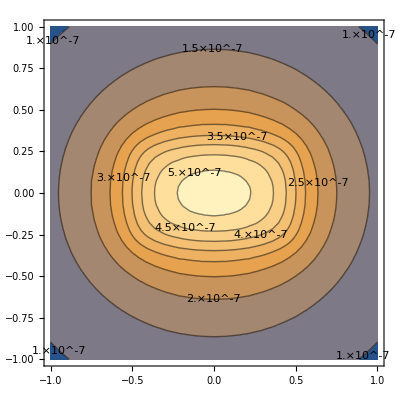

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

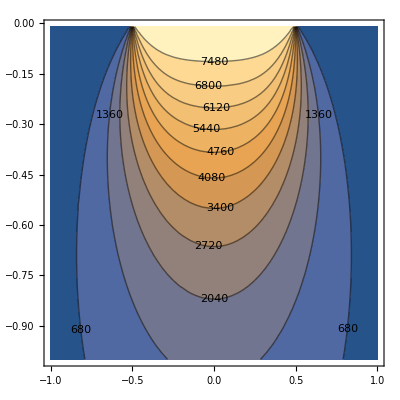

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

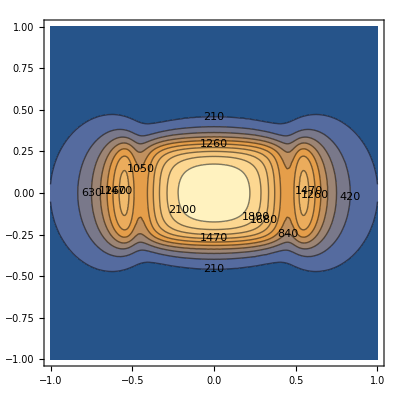

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

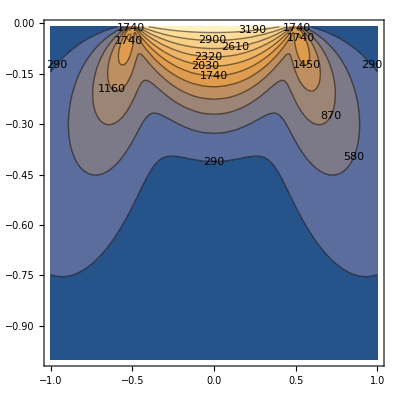

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

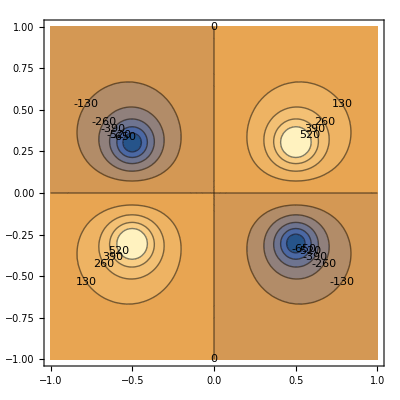

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

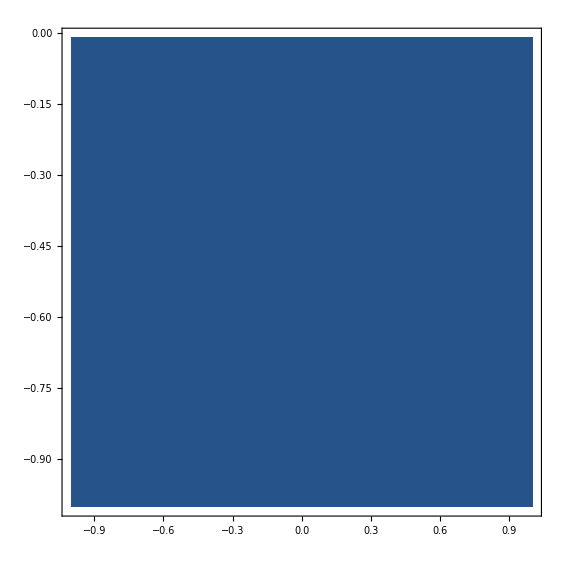

```mathematica
Print[ContourPlot[σ[1,2,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

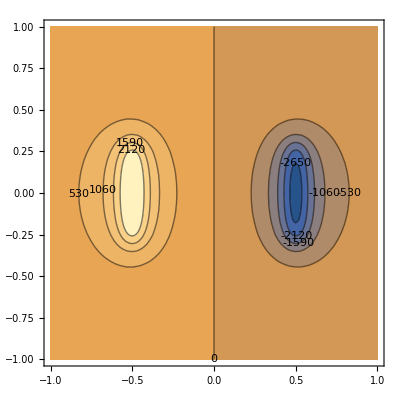

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

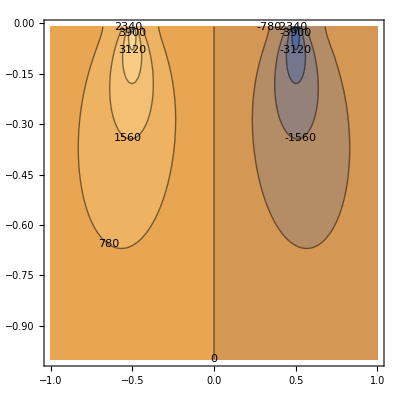

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

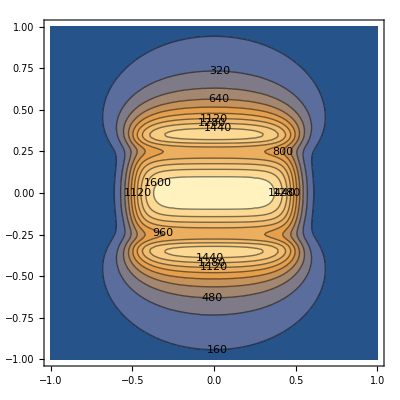

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

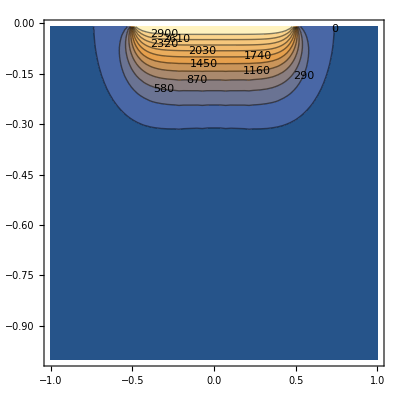

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

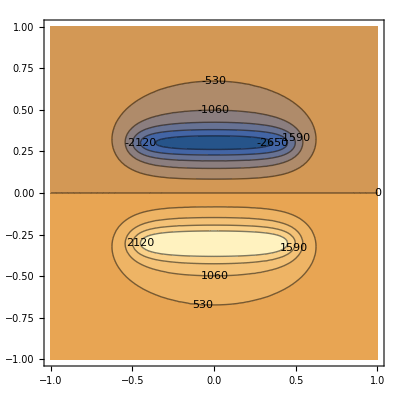

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

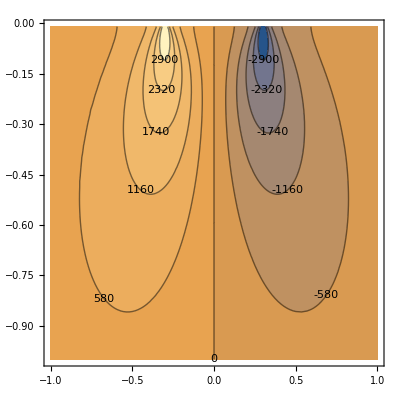

```mathematica
Print[ContourPlot[σ[2,3,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

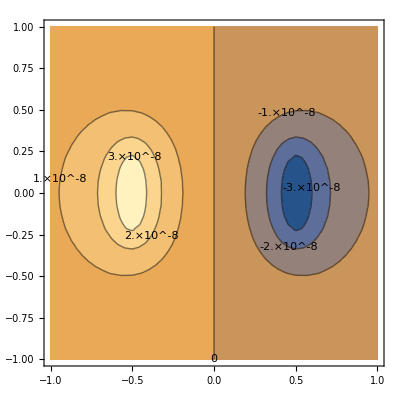

```mathematica
Print[ContourPlot[U[1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

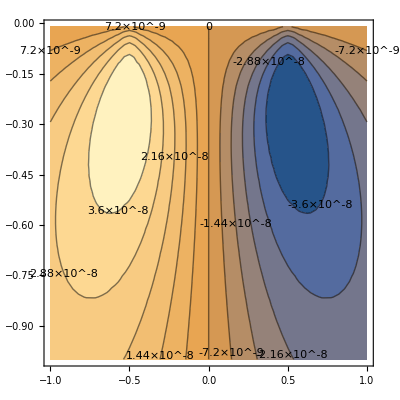

```mathematica
Print[ContourPlot[U[1,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

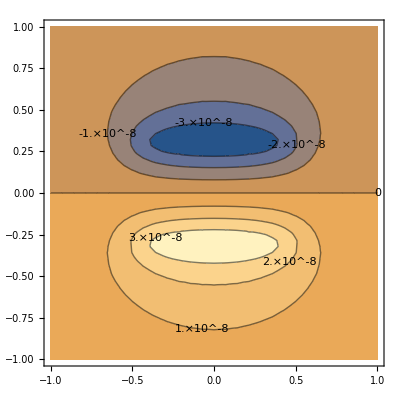

```mathematica
Print[ContourPlot[U[2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

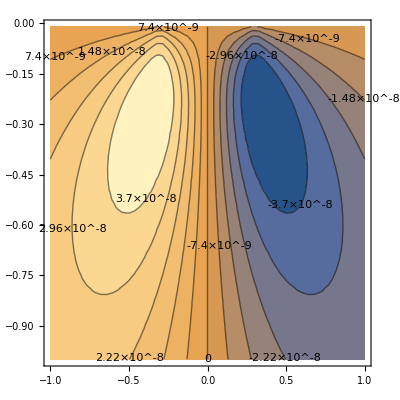

```mathematica
Print[ContourPlot[U[2,3][a/2,a,y+b/2,b,z,P0,λ,μ] ,{y,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

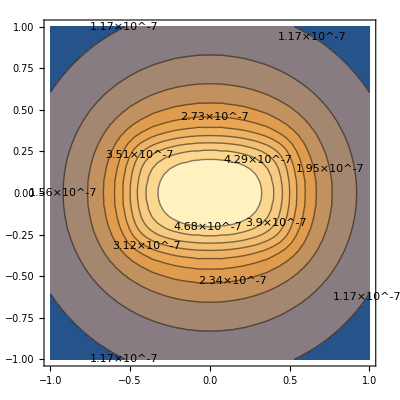

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

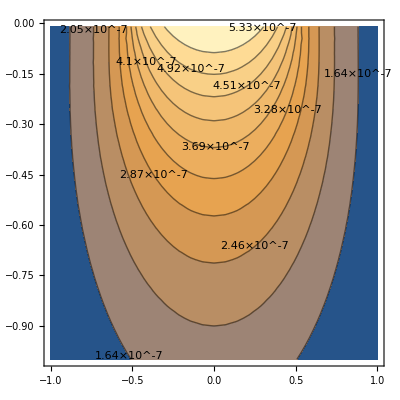

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

## 2) Граничная задача для вдавливания плоского эллиптического штампа

#### Графики функции поверхностного распределения и её дискретизации

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
ListPlot3D[DisplacementTab,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
BoundaryElements=Table[{X[[xi]],Y[[yj]],DisplacementTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
```

### Получение решения последовательно

```mathematica
PressureSP[xj_,yj_]:=Table[σ[3,3,3][X[[m]]-xj,a,Y[[o]]-yj,b,U0,p0,λ,μ],{m,1,n},{o,1,n}];
```

```mathematica
(*AbsoluteTiming[Equationq=Flatten[Table[PressureSP[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];]
```

Syntax::tsntxi: "(*AbsoluteTiming[Equationq=Flatten[Table[PressureSP[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];]" is incomplete; more input is needed.

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
B=FPT=Flatten[DisplacementTab];
Equationq=Flatten[Table[Sum[σ[3,3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,U0,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];
```

```mathematica
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,Filling->Axis,InterpolationOrder->0,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntSRes:=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n σ[3,3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*SolN1q[[i,j]]];
```

```mathematica
Resq=Table[DIntSRes[X[[i]],Y[[j]],U0],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*CUDAQ[] *)
```

```mathematica
(*CUDAResourcesInstall[]*)
```

```mathematica
(*Table[U[3,3][X[[i]]-X[[1]],h,Y[[i]]-Y[[1]],h,0.01,p0,λ,μ],{i,1,n},{j,1,n}]//MatrixForm*)
```

## 3)Перемещения внутри эллипса заданы

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];,
a;
(*Print["i: ",i," j: ",j]*)];

]]
Print["Amount of Boundary elements inside ellipse is: ",amount]
Ak = Table[Subscript[q, k],{k,1,amount}];
DisV[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,U0,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

Amount of Boundary elements inside ellipse is: 76

```mathematica
Equation2=Table[DisV[X[[Mp[[i,1]]]],Y[[Mp[[i,2]]]]]==U0,{i,1,amount}];
Solq=Solve[Equation2,Ak];
```

```mathematica
SolutionValues=Table[Solq[[1,i,2]],{i,1,amount}];
```

```mathematica
(*добавление столбца со значениями, выполнять только один раз*)
Tmp=Transpose[Mp];
AppendTo[Tmp,SolutionValues];
Mp=Transpose[Tmp];
```

```mathematica
FinalList=Table[0,{i,1,n},{j,1,n}];
```

```mathematica
Table[FinalList[[Mp[[i,1]],Mp[[i,2]]]]=Mp[[i,3]],{i,1,amount}];(*в необходимые места подставляем полученные значения, остальные приравниваем 0, для того, чтобы построить 3-х мерный график*)
```

```mathematica
ListPlot3D[FinalList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntURes[x_,y_,z_]:=If[(x/a)^2+(y/b)^2≤1,∑_(i=1)^n ∑_(j=1)^n U[3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*FinalList[[i,j]],0];
ResU=Table[DIntURes[X[[i]],Y[[j]],U0],{i,1,n},{j,1,n}];
ListPlot3D[ResU,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

## 4) Parallel 2)

```mathematica
AbsoluteTiming[A={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
A=AppendTo[A,Flatten[PressureSP[X[[i]],Y[[j]]]]];]]
]
```

{0.364731,Null}

```mathematica
Ainv=Inverse[A];
```

```mathematica
sf=Dot[B, Ainv];
```

```mathematica
SolN1q = Table[sf[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];
(*Print["i: ",i," j: ",j]*)];

]]
Print["Amount of Boundary elements inside ellipse is: ",amount]
Ak = Table[Subscript[q, k],{k,1,amount}];
DisZ[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,U0,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

Amount of Boundary elements inside ellipse is: 76

```mathematica
Equation2=Table[DisV[X[[Mp[[i,1]]]],Y[[Mp[[i,2]]]]]==U0,{i,1,amount}];
Solq=Solve[Equation2,Ak];
```

```mathematica
SolutionValues=Table[Solq[[1,i,2]],{i,1,amount}];
```

```mathematica
(*добавление столбца со значениями, выполнять только один раз*)
Tmp=Transpose[Mp];
AppendTo[Tmp,SolutionValues];
Mp=Transpose[Tmp];
```

```mathematica
FinalList=Table[0,{i,1,n},{j,1,n}];
```

```mathematica
Table[FinalList[[Mp[[i,1]],Mp[[i,2]]]]=Mp[[i,3]],{i,1,amount}];(*в необходимые места подставляем полученные значения, остальные приравниваем 0, для того, чтобы построить 3-х мерный график*)
```

```mathematica
ListPlot3D[FinalList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
SolN1q//MatrixForm
```

(-1.21824×10^-8 | 1.13639×10^-8 | -1.22522×10^-8 | 1.13088×10^-8 | -3.63682×10^-8 | 5.74542×10^-8 | -8.24917×10^-8 | 1.03348×10^-7 | -1.7618×10^-7 | 2.87361×10^-7 | -4.50414×10^-7 | 6.5084×10^-7 | -9.98119×10^-7 | 1.55938×10^-6 | -2.44412×10^-6 | 3.71597×10^-6 | -5.67491×10^-6 | 8.72449×10^-6 | -0.0000135273 | 0.0000207481
1.13513×10^-8 | -1.06203×10^-8 | 1.14098×10^-8 | -1.05697×10^-8 | 3.38884×10^-8 | -5.3637×10^-8 | 7.69547×10^-8 | -9.64525×10^-8 | 1.64332×10^-7 | -2.68248×10^-7 | 4.20245×10^-7 | -6.07656×10^-7 | 9.31333×10^-7 | -1.45587×10^-6 | 2.2813×10^-6 | -3.46964×10^-6 | 5.2977×10^-6 | -8.14712×10^-6 | 0.0000126281 | -0.0000193864
-1.22575×10^-8 | 1.14246×10^-8 | -1.23245×10^-8 | 1.13726×10^-8 | -3.65817×10^-8 | 5.78298×10^-8 | -8.29167×10^-8 | 1.04132×10^-7 | -1.77079×10^-7 | 2.89181×10^-7 | -4.5316×10^-7 | 6.54982×10^-7 | -1.00454×10^-6 | 1.56908×10^-6 | -2.45964×10^-6 | 3.73993×10^-6 | -5.71183×10^-6 | 8.78204×10^-6 | -0.0000136149 | 0.0000208887
1.12876×10^-8 | -1.05687×10^-8 | 1.13471×10^-8 | -1.05126×10^-8 | 3.372×10^-8 | -5.32847×10^-8 | 7.6785×10^-8 | -9.51331×10^-8 | 1.65697×10^-7 | -2.68196×10^-7 | 4.19868×10^-7 | -6.05278×10^-7 | 9.29698×10^-7 | -1.45796×10^-6 | 2.28458×10^-6 | -3.47057×10^-6 | 5.29884×10^-6 | -8.1575×10^-6 | 0.0000126597 | -0.0000194564
-1.23221×10^-8 | 1.14759×10^-8 | -1.23888×10^-8 | 1.14294×10^-8 | -3.67478×10^-8 | 5.82422×10^-8 | -8.25776×10^-8 | 1.08582×10^-7 | -3.13481×10^-6 | 3.24939×10^-6 | -3.41254×10^-6 | 3.62225×10^-6 | -6.86741×10^-6 | 0.0000132117 | -0.0000198867 | 0.0000269676 | -0.0000404685 | 0.0000664307 | -0.000105437 | 0.000158235
1.12179×10^-8 | -1.05152×10^-8 | 1.1277×10^-8 | -1.04566×10^-8 | 3.35269×10^-8 | -5.28735×10^-8 | 7.83113×10^-8 | -3.05214×10^-6 | 9.02591×10^-6 | -9.13237×10^-6 | 9.28669×10^-6 | -0.0000153099 | 0.0000271677 | -0.0000420475 | 0.000060185 | -0.0000902199 | 0.000143546 | -0.00022599 | 0.000343978 | -0.000520225
-1.25045×10^-8 | 1.16306×10^-8 | -1.25717×10^-8 | 1.15862×10^-8 | -3.73412×10^-8 | 5.91386×10^-8 | -8.63356×10^-8 | 3.06466×10^-6 | -9.04878×10^-6 | 9.16675×10^-6 | -9.33794×10^-6 | 0.0000153872 | -0.0000272944 | 0.000042245 | -0.0000604942 | 0.0000906888 | -0.000144289 | 0.000227147 | -0.000345786 | 0.000523128
-1.28366×10^-8 | 1.19197×10^-8 | -1.29302×10^-8 | 1.18744×10^-8 | -3.80429×10^-8 | 6.04842×10^-8 | -8.28029×10^-8 | -2.85507×10^-6 | 8.68728×10^-6 | -8.57535×10^-6 | 8.41396×10^-6 | -0.0000140639 | 0.0000252664 | -0.0000390705 | 0.0000555137 | -0.0000831546 | 0.000132808 | -0.000209541 | 0.000318398 | -0.00048158
3.39709×10^-8 | -3.18236×10^-8 | 3.41658×10^-8 | -3.16607×10^-8 | 1.01248×10^-7 | -1.57563×10^-7 | -2.72796×10^-6 | 8.57969×10^-6 | -0.0000142896 | 0.0000139896 | -0.0000193832 | 0.0000362774 | -0.0000584089 | 0.0000798311 | -0.000114873 | 0.00018614 | -0.000300758 | 0.000457224 | -0.000682538 | 0.0010468
-5.958×10^-8 | 5.55611×10^-8 | -5.99545×10^-8 | 5.52745×10^-8 | -1.77496×10^-7 | 2.78176×10^-7 | 2.55695×10^-6 | -8.36824×10^-6 | 0.0000139242 | -0.0000133925 | 0.0000184494 | -0.0000349414 | 0.0000563597 | -0.0000766248 | 0.00010984 | -0.000178529 | 0.000289158 | -0.000439435 | 0.000654861 | -0.00100482
8.04682×10^-8 | -7.53014×10^-8 | 8.09089×10^-8 | -7.49752×10^-8 | 2.39638×10^-7 | -3.77132×10^-7 | -2.41563×10^-6 | 8.19075×10^-6 | -0.0000136454 | 0.0000129226 | -0.0000177033 | 0.0000338499 | -0.0000547136 | 0.0000740822 | -0.000105865 | 0.000172448 | -0.0002799 | 0.000425291 | -0.00063306 | 0.000971379
-1.06308×10^-7 | 9.91838×10^-8 | -1.0697×10^-7 | 9.86397×10^-8 | -3.16908×10^-7 | 4.97384×10^-7 | 2.2405×10^-6 | -7.98604×10^-6 | 7.46998×10^-6 | -6.51018×10^-6 | 0.0000109436 | -0.0000267133 | 0.0000412502 | -0.0000481956 | 0.0000668713 | -0.000119646 | 0.000200864 | -0.000295776 | 0.000427749 | -0.00066359
1.26975×10^-7 | -1.1879×10^-7 | 1.27666×10^-7 | -1.18293×10^-7 | 3.78043×10^-7 | -5.98145×10^-7 | 8.58913×10^-7 | -3.95312×10^-6 | 0.000016282 | -0.0000174501 | 0.0000191348 | -0.0000268325 | 0.0000471209 | -0.0000779712 | 0.000115014 | -0.000167065 | 0.000258742 | -0.000410264 | 0.00063387 | -0.000955691
-1.53442×10^-7 | 1.43185×10^-7 | -1.54377×10^-7 | 1.42428×10^-7 | -4.57524×10^-7 | 7.21208×10^-7 | -1.04586×10^-6 | 0.0000100397 | -0.0000342196 | 0.000035635 | -0.000037694 | 0.0000573684 | -0.000101164 | 0.000161488 | -0.000234619 | 0.000346343 | -0.000543732 | 0.000858371 | -0.00131546 | 0.00198612
1.2675×10^-7 | -1.18622×10^-7 | 1.27379×10^-7 | -1.18117×10^-7 | 3.78224×10^-7 | -5.98132×10^-7 | 8.48594×10^-7 | -0.000015634 | 0.0000513467 | -0.0000525422 | 0.0000542002 | -0.0000848759 | 0.000150532 | -0.000237847 | 0.000342992 | -0.000508395 | 0.000802104 | -0.0012657 | 0.0019338 | -0.00291957
-6.12604×10^-8 | 5.69867×10^-8 | -6.15825×10^-8 | 5.66569×10^-8 | -1.83769×10^-7 | 2.96404×10^-7 | -6.27151×10^-6 | 0.0000355929 | -0.000085575 | 0.0000862031 | -0.0000985612 | 0.000168425 | -0.000286374 | 0.000424489 | -0.000610361 | 0.000939284 | -0.0014986 | 0.00232648 | -0.00351704 | 0.00534124
-5.77796×10^-8 | 5.38287×10^-8 | -5.83408×10^-8 | 5.34423×10^-8 | -1.70558×10^-7 | 2.53939×10^-7 | 0.0000113296 | -0.0000521616 | 0.00011608 | -0.000115673 | 0.000138004 | -0.000240402 | 0.000403368 | -0.000587092 | 0.000844057 | -0.00131389 | 0.00210182 | -0.0032473 | 0.00489408 | -0.00744838
2.15273×10^-7 | -2.01533×10^-7 | 2.16693×10^-7 | -2.00594×10^-7 | 6.38475×10^-7 | -9.88288×10^-7 | -0.0000161311 | 0.0000683912 | -0.00014318 | 0.000141372 | -0.000173188 | 0.000307451 | -0.000511637 | 0.000733689 | -0.0010536 | 0.00165475 | -0.00265451 | 0.0040863 | -0.00614292 | 0.00936177
-4.26801×10^-7 | 3.98675×10^-7 | -4.29616×10^-7 | 3.9663×10^-7 | -1.26784×10^-6 | 1.9725×10^-6 | 0.0000205918 | -0.0000843044 | 0.000158174 | -0.000154477 | 0.00019511 | -0.000360765 | 0.000594011 | -0.000830242 | 0.00118761 | -0.00189412 | 0.00305584 | -0.004678 | 0.00699873 | -0.0106902
6.74838×10^-7 | -6.31395×10^-7 | 6.79344×10^-7 | -6.28276×10^-7 | 2.00547×10^-6 | -3.13299×10^-6 | -0.0000189076 | 0.0000765029 | -0.000126107 | 0.000120149 | -0.000157497 | 0.000307999 | -0.000501563 | 0.000677573 | -0.000962668 | 0.00156729 | -0.0025502 | 0.00387688 | -0.00576383 | 0.00882716)